```mathematica
Clear["Global`*"]
```

# Difference

## Cory Aitchison - February 2022

Examine the difference between the numerical and the ansatz near the origin

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param  /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
taylorests[0] = {A->0.033327514775158475,B->1.153359200278144};
taylorests[1] = {A->0.24242264239512362,B->0.8985343791605391};
taylorests[3] = {A->0.33494186742400267,B->0.6945601303275413};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

### Long data

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
```

```mathematica
fdata = Interpolation[data];
fdata4[x_] := 4σ^4 fdata[x]+ Γ fdata[x]^3 /. param;
```

## Plots

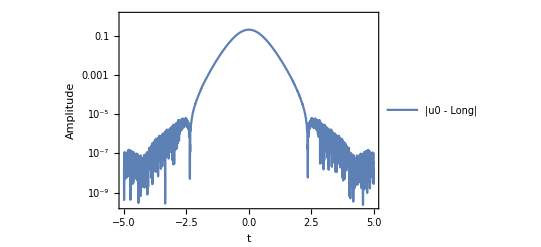

```mathematica
p0 = LogPlot[Abs[u[0][x] - fdata[x]] /. param /. estimates, {x,-5,5}, Frame->True, PlotLegends->{"|u0 - Long|"}, FrameLabel->{t, Amplitude}]
```

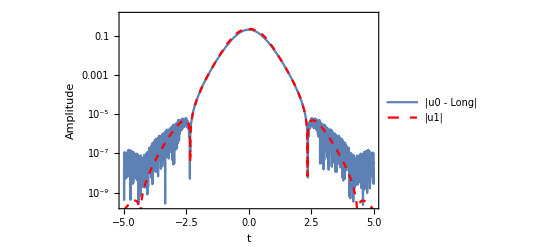

```mathematica
Show[p0, LogPlot[Abs[u[1][x]]  /. answer[1] /. param/. estimates, {x,-5,5}, PlotStyle->{Red, Dashed, Thick}, PlotLegends->{"|u1|"}]]
```

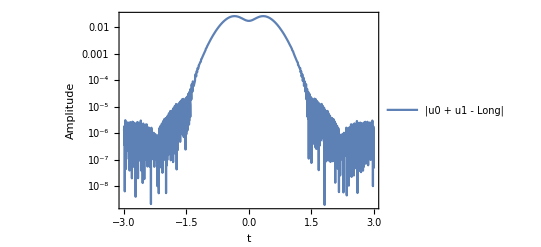

```mathematica
p1 = LogPlot[Abs[-FinalFunction[1] + fdata[x]]/. param /. estimates, {x,-3,3}, Frame->True, PlotLegends->{"|u0 + u1 - Long|"}, FrameLabel->{t, Amplitude}]
```

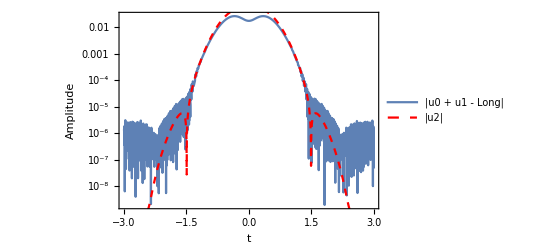

```mathematica
Show[p1, LogPlot[Abs[SubAnswers[u[2][x], 3] ]/. param/. estimates, {x,-5,5}, PlotStyle->{Red, Dashed, Thick}, PlotLegends->{"|u2|"}]]
```

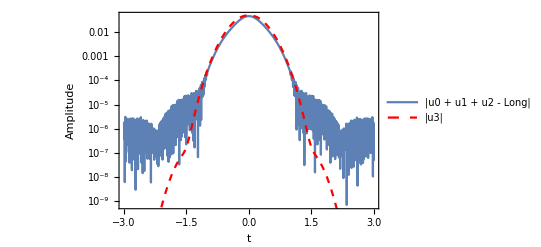

```mathematica
Show[LogPlot[Abs[FinalFunction[2] - fdata[x]]/. param /. estimates, {x,-3,3}, Frame->True, PlotLegends->{"|u0 + u1 + u2 - Long|"}, FrameLabel->{t, Amplitude}], LogPlot[Abs[SubAnswers[u[3][x], 4]] /. param/. estimates, {x,-5,5}, PlotStyle->{Red, Dashed, Thick}, PlotLegends->{"|u3|"}]]
```

## Gaussian

```mathematica
gausu[x_]:=(u[0][x]) /(1 +0.81Exp[-x^2]);
gausg[x_]:=(0.82Exp[-1.874x^2]) /(1 +0.81Exp[-x^2]);
gaus[x_]:=(u[0][x]+0.82 Exp[-1.874 x^2])/(1+0.81 Exp[-x^2]);
```

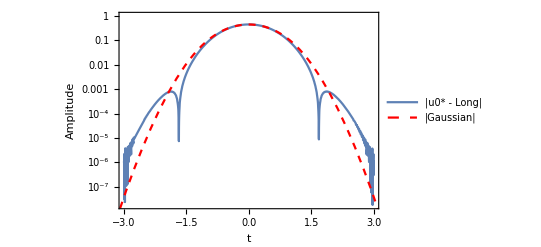

```mathematica
Show[LogPlot[Abs[gausu[x] - fdata[x]]/. param /. estimates, {x,-3,3}, Frame->True, PlotLegends->{"|u0* - Long|"}, FrameLabel->{t, Amplitude}], LogPlot[Abs[gausg[x]] /. param/. estimates, {x,-5,5}, PlotStyle->{Red, Dashed, Thick}, PlotLegends->{"|Gaussian|"}]]
```